# Reverse Dictionary

## Data

Data was taken from the site of the following paper: Hill, F. Cho, KH., Korhonen, A., and Bengio, Y. Learning to Understand Phrases by Embedding the Dictionary. 2016. Transactions of the Association for Computational Linguistics (TACL). Originally it was recollected via WordNik API in Python.

## Proof of Concept

For this first proof of concept analysis, we used 50 of the most common nouns in the English language. We chose the 50 with more definitions assigned to them so that the training can be more efficient. The number of definitions per word was normalized to the minimum among the maximum number of definitions for each word. This was so there would be no bias in the data.

Global Set

```mathematica
rawData=Import["Personal\\WSS\\wss_project\\training_data\\60Def50Words.csv"];
```

```mathematica
associate[elem_]:=Last[elem]-> First[elem];
```

```mathematica
wordDefSet=Map[associate, rawData];
RandomSample[wordDefSet, 10]//TableForm
```

to wait on as a manservant→man
 nightfall→night
 the backbone or spine→back
 a unit of relative proportion in a mixture→part
 home plate→home
 a male ancestor more remote than a parent a progenitor especially a first ancestor a founder of a race or family in the plural fathers ancestors→father
 a product of equal factors→power
 style may be essentially the same as appellation but it is now generally limited to a name assumed or assigned for public use as the style of his most christian majesty they transacted business under the firm style of smith co→name
 of or having to do with a family family problems→family
 of or relating to school or education in schools school supplies a school dictionary→school

```mathematica
wordset=DeleteDuplicates[Map[Last,wordDefSet]];
```

Testing Set

```mathematica
testingSet=Select[Normal[DeleteDuplicates[Association[RandomSample[wordDefSet]]]],Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[testingSet, 10]//TableForm
```

that which happens without human design or forethought chance accident hazard fortune fate→lot
 a large number or amount→power
 the passenger carrying portion of certain amusement park rides such as ferris wheels→car
 one who presides one who superintends and directs the proceedings of others a ruler a ruling spirit→president
 an established political group organized to promote and support its principles and candidates for public office→party
 to line or trim the edge of especially with contrasting material face a hem with lace→face
 parents with their children whether they dwell together or not in a more general sense any group of persons closely related by blood as parents children uncles aunts and cousins often used in a restricted sense only of a group of parents and children founded upon the principle of monogamy→family
 indicating the position of something in a list or sequence→number
 a creative source an origin philosophy is the mother of the sciences→mother
 to compel through pressure or necessity i forced myself to practice daily→force

Training Set

```mathematica
trainingSet=Select[wordDefSet,Not[MemberQ[testingSet,First[#]->_]]&&Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[trainingSet, 10]//TableForm
```

the crisis or culminating point as of a disease that point in the growth or course of a thing at which decline begins→state
 a manner or way of performing something a light hand with makeup→hand
 a theatre building or the audience for a live theatrical or similar performance→house
 those hours or the daily recurring period allotted by usage or law for work→day
 a name given to several trees and shrubs of the genus pyrus as pyrus domestica and p→service
 a female child from birth to the age of puberty a young maiden→girl
 a loose affiliation of gangsters in charge of organized criminal activities→family
 one possible aspect of a concept→side
 at someone s service ready to help or be of use→service
 to guide a missile or aircraft to a target automatically→home

Simplest Approach

Simplest Approach consists of using built in function Classify to attempt to solve the problem.

```mathematica
cl=Classify[trainingSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[cl,testingSet]
```

ClassifierMeasurementsObject[…]

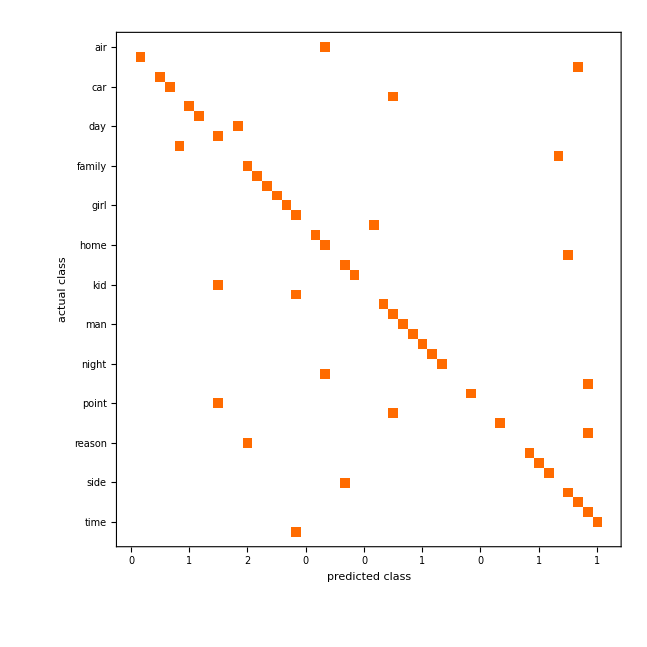

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
ClassifierInformation[cl]
```

Classifier information
Method | Markov
Number of classes | 50
Number of features | 1
Number of training examples | 2940
Number of tokens | 5692
Markov order | 1
Regularization method | Katz

Apparently this does it, and the performance seems pretty good. Now, this model might be over-fitted, so we must test with data it has never seen.

```mathematica
ClassifierMeasurements[cl,testingSet,"Accuracy"]
```

0.64

```mathematica
ClassifierMeasurements[cl,testingSet,"F1Score"]
```

<|air→0.,back→1.,book→0.,business→1.,car→1.,case→0.,change→1.,company→1.,day→0.,end→0.5,eye→0.,face→0.,family→0.666667,father→1.,force→1.,game→1.,girl→1.,group→0.5,hand→0.,head→1.,home→0.5,house→0.,issue→0.666667,job→1.,kid→0.,law→0.,level→1.,lot→0.5,man→1.,minute→1.,mother→1.,name→1.,night→1.,number→0.,part→0.,party→1.,point→0.,power→0.,president→1.,question→0.,reason→0.,right→1.,school→1.,service→1.,side→0.,state→0.666667,study→0.666667,thing→0.5,time→1.,word→0.|>

Test with own definitions

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@cl[text,"TopProbabilities"->3]]
```

## Complete Data Set

Training Set

```mathematica
rawData=Import["Personal\\WSS\\wss_project\\training_data\\training_data.csv"];
```

```mathematica
trainingSet=Map[associate, rawData];
RandomSample[trainingSet,10]//TableForm
```

to hurry oneself→hie
 a small sharp antipersonnel projectile used as shrapnel fired from a shotgun or scattered from an aircraft→flechette
 each union has a common workhouse and all the cost of the relief of the poor is charged upon the common fund→union
 spread over a large area of a body tissue or organ→disseminated
 the metal lead→saturn
 the emperor of japan→tenno
 it has been one of the most useful types of stone to humankind→flint
 to touch lightly to toy with→dinger
 an asian vine grown as a root starch and sometimes considered a noxious weed→kudzu
 in bibliography a collection of different works either by one or several authors→polygraph

```mathematica
Length[trainingSet]
```

852471

```mathematica
wordset=DeleteDuplicates[Map[Last,trainingSet]];
Length[wordset]
```

67713

Testing Set

```mathematica
rawTesting=Import["Personal\\WSS\\wss_project\\test_data\\testing_data.csv"];
```

```mathematica
testingSet=Map[associate, rawTesting];
RandomSample[testingSet, 10]//TableForm
```

a popular alcoholic drink made with grapes→wine
 a type of classical musical performance in which performers sing and act→opera
 a flat table for working at often found in an office→desk
 something that has been cleaned with water recently→washed
 a machine used for talking when two people are not in the same place→telephone
 to start a process or a programme or an action→begin
 to choose between more than one options or possibilities→decide
 a material that is normally white made from trees and useful for writing on→paper
 something that makes you happy or makes you laugh→fun
 the circular parts of cars or vehicles designed to roll along the ground→wheel

Simplest Approach

As it proved to be working for the small dataset, we can try again with Classify.

```mathematica
cl=Classify[trainingSet]
```

Neural Network?

```mathematica
classes=wordset;
```

```mathematica
dec=NetDecoder[{"Class",classes}]
```

NetDecoder[<>]

```mathematica
embedding=NetModel["GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword-5 Data"]
```

EmbeddingLayer[<>]

```mathematica
chain=NetChain[
{embedding,GatedRecurrentLayer[32],
LongShortTermMemoryLayer[32],
SequenceLastLayer[],
LinearLayer[Length[classes]],
SoftmaxLayer[]}]
```

NetChain[]

```mathematica
net=NetGraph[
<|
"embedding"-> {embedding,GatedRecurrentLayer[32]},
"classifier"-> {LongShortTermMemoryLayer[32],DropoutLayer[0.3],SequenceLastLayer[],LinearLayer[Length[classes]],SoftmaxLayer[]}
|>
,{NetPort["Input"]-> "embedding"-> "classifier"-> NetPort["Output"]},
"Output"-> dec]
```

NetGraph[]

```mathematica
trainedNet=NetTrain[net,trainingSet,ValidationSet->testingSet,
MaxTrainingRounds->50,TargetDevice->"GPU"]
```

Test with own definitions

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@cl[text,"TopProbabilities"->3]]
```